## Белко Владислав, ПО-5

Лабораторная работа №6.

## Visualization & Graphics

### Data Visualization / Function Visualization

ListPlot

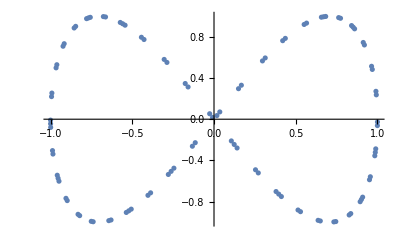

```mathematica
ListPlot[Table[{Sin[n],Sin[2n]},{n,100}]]
```

ListLinePlot

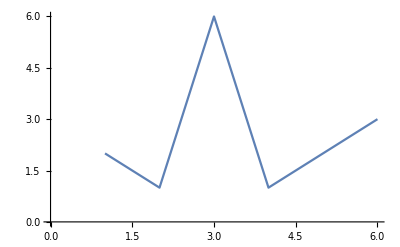

```mathematica
ListLinePlot[{2,1,6,1,2,3}]
```

```mathematica
ListStepPlot
```

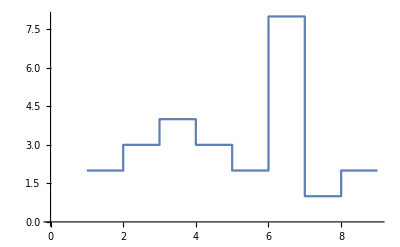

```mathematica
ListStepPlot[{2,3,4,3,2,8,1,2}]
```

```mathematica
ListPlot3D
```

```mathematica
ListPlot3D[{{0,0,1},{1,0,0},{0,1,0}},Mesh->All]
```

-Graphics3D-

```mathematica
ListDensityPlot
```

```mathematica
ListDensityPlot[{{0,0,1},{1,0,0},{0,1,0}},Mesh->All]
```

-Graphics-

```mathematica
ListCurvePathPlot
```

```mathematica
data=Table[{Cos[t],Sin[t]},{t,RandomReal[{0,2Pi},50]}];
```

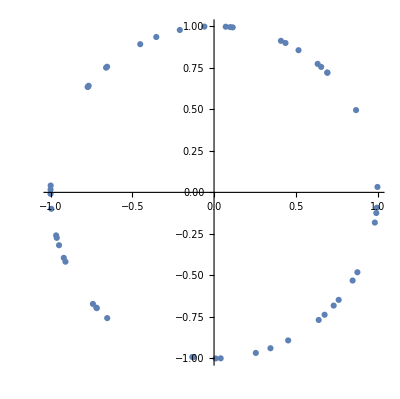

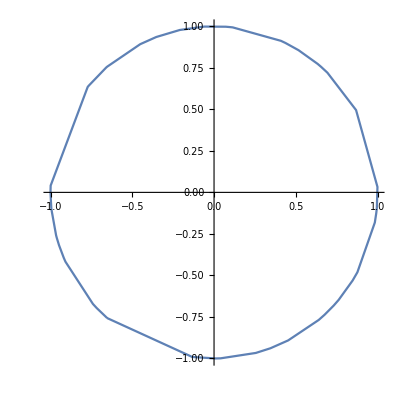

```mathematica
ListPlot[data,AspectRatio->Automatic]
ListCurvePathPlot[data]
```

```mathematica
ArrayPlot
```

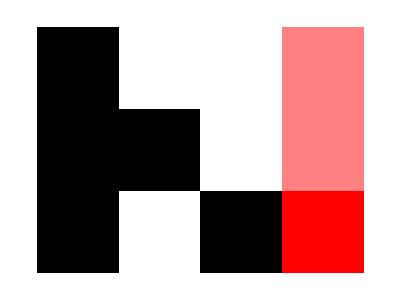

```mathematica
ArrayPlot[{{1,0,0,Pink},{1,1,0,Pink},{1,0,1,Red}}]
```

```mathematica
DateListPlot
```

```mathematica
data={{DateObject[{2016,10,1},"Day","Gregorian",-5.],10},{DateObject[{2016,10,15},"Day","Gregorian",-5.],17},{DateObject[{2016,10,30},"Day","Gregorian",-5.],15},{DateObject[{2016,11,20},"Day","Gregorian",-5.],20}};
```

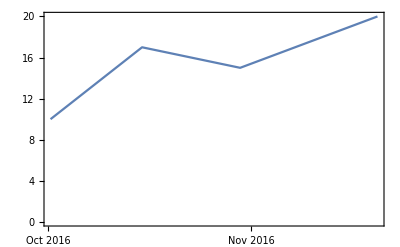

```mathematica
DateListPlot[data]
```

```mathematica
GraphPlot
```

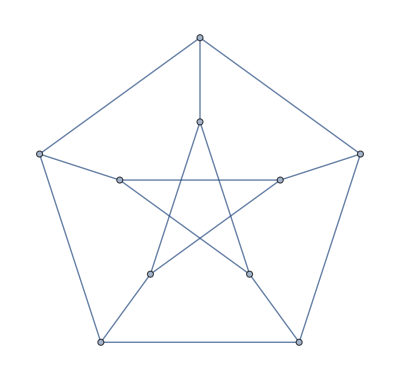

```mathematica
GraphPlot[PetersenGraph[]]
```

```mathematica
PlotLabels
```

```mathematica
ListLinePlot[{{1,2,3,5,8,13,21},{1,2,4,8,16,32,64}},PlotLabels->{"Fibonacci","Powers"}]
```

-Graphics-

```mathematica
RegionPlot
```

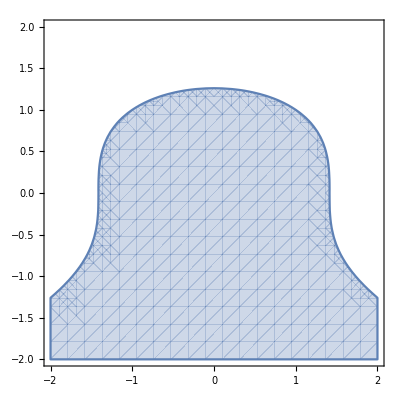

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

### Charting and Information Visualization

```mathematica
BarChart
```

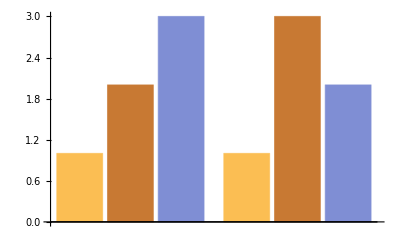

```mathematica
BarChart[{{1,2,3},{1,3,2}}]
```

```mathematica
PieChart
```

```mathematica
PieChart[{1,2,3,4}]
```

-Graphics-

```mathematica
BarChart3D
```

```mathematica
BarChart3D[{{1,2,3},{1,3,2}}]
```

-Graphics3D-

```mathematica
SectorChart3D
```

```mathematica
SectorChart3D[{{2,2,2},{2,2,2},{3,3, 3}}]
```

-Graphics3D-

```mathematica
Histogram
```

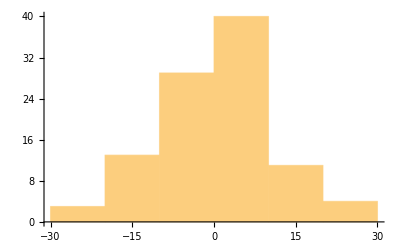

```mathematica
Histogram[RandomVariate[NormalDistribution[0,10],100]]
```

```mathematica
SectorChart3D
```

```mathematica
GeoGraphics[Polygon[Entity["Country","Belarus"]]]
```

-Graphics-

```mathematica
Animate
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5}]
```

```mathematica
Grid
```

```mathematica
Grid[{{a,b,c},{х,у^2,z^3}},Frame->All]
```

a | b | c
х | у^2 | z^3

```mathematica
GeoPath
```

```mathematica
GeoGraphics[Arrow@GeoPath[{Entity["City",{"Brest","Brest","Belarus"}],4000,120},"Geodesic"]]
```

-Graphics-

```mathematica
SectorChart3D
```

```mathematica
InteractiveTradingChart[{"GOOGL",{{2009,1,1},{2009,12,31}}}]
```

### Charting and Information Visualization

```mathematica
GeoListPlot
```

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant}]
```

-Graphics-

```mathematica
GeoBubbleChart
```

```mathematica
data={Entity["Country","Argentina"]->Quantity[41827217, "People"],Entity["Country","Bolivia"]->Quantity[10573218, "People"],Entity["Country","Brazil"]->Quantity[201700544, "People"],Entity["Country","Chile"]->Quantity[17722868, "People"],Entity["Country","Colombia"]->Quantity[48770570, "People"],Entity["Country","Ecuador"]->Quantity[15255149, "People"],Entity["Country","FalklandIslands"]->Quantity[2840, "People"],Entity["Country","FrenchGuiana"]->Quantity[249408, "People"],Entity["Country","Guyana"]->Quantity[760972, "People"],Entity["Country","Paraguay"]->Quantity[6913774, "People"],Entity["Country","Peru"]->Quantity[30418591, "People"],Entity["Country","Suriname"]->Quantity[543497, "People"],Entity["Country","Uruguay"]->Quantity[3415252, "People"],Entity["Country","Venezuela"]->Quantity[30786062, "People"]};
```

```mathematica
GeoBubbleChart[data,GeoRange->LinguisticAssistant]
```

-Graphics-

```mathematica
DynamicGeoGraphics
```

```mathematica
DynamicGeoGraphics[]
```

```mathematica
GeoPosition
```

```mathematica
GeoPosition[Entity["City", {"Brest", "Brest", "Belarus"}]]
```

GeoPosition[{52.12,23.68}]

```mathematica
SectorChart3D
```

```mathematica
cities=CityData[{Large,"Belarus"}]
```

{Minsk,Homjel,Mahiljow,Vitebsk,Hrodna,Brest,Babrujsk,Baranavicy,Barisaw,Pinsk,Orsha,Mazyr,Salihorsk,Navapolack}

```mathematica
SectorChart3D
```

```mathematica
GeoGraphics[Entity["City",{"Brest","Brest","Belarus"}],GeoScaleBar->{"Imperial","Metric"}]
```

-Graphics-

### Dynamic Visualization

```mathematica
Manipulate
```

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
ListAnimate
```

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
TabView
```

```mathematica
TabView[{х->a,у->b,z->c}]
```

123

```mathematica
SlideView
```

```mathematica
SlideView[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
FlipView
```

```mathematica
FlipView[{х+у,a+b}]
```

```mathematica
Mouseover
```

```mathematica
Mouseover[off,on]
```

```mathematica
Slider
```

```mathematica
{Slider[Dynamic[n],{0,100,1}],Dynamic[n]}
```

{,}

```mathematica
Slider2D
```

```mathematica
{Slider2D[Dynamic[r]],Dynamic[r]}
```

{,}

### Graphics Options & Styling

```mathematica
AspectRatio
```


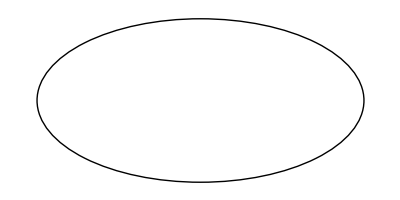
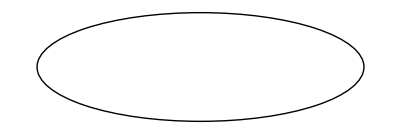

```mathematica
Table[Graphics[Circle[],AspectRatio->1/k],{k,1,3}]
```

```mathematica
Mesh
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->5]
```

-Graphics3D-

```mathematica
ColorData
```

```mathematica
ColorData["TemperatureMap"]
```

ColorDataFunction[…]

### Graphics Options & Styling

```mathematica
Direct Interactive Drawing & Editing
```

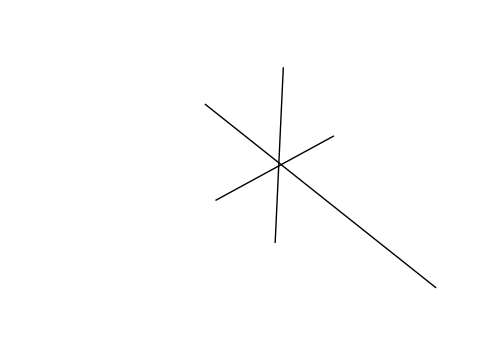

### Symbolic Graphics Language

```mathematica
Basic 2D/3D Objects - text
```

```mathematica
Text["x^2+2x+1==0"]
```

x^2+2x+1==0

```mathematica
Special 2D/3D Objects - Circle
```

```mathematica
Graphics[Circle[]]
```

-Graphics-

```mathematica
Special 3D Objects - Cuboid
```

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

```mathematica
Directives - RGBColor
```

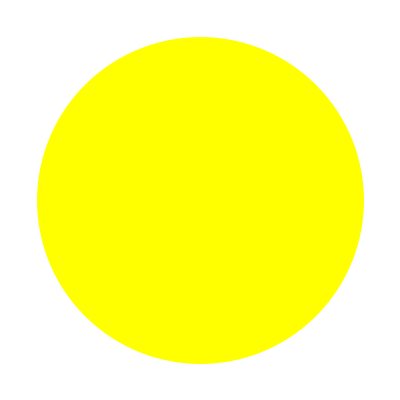

```mathematica
Graphics[{RGBColor[1,1,0],Disk[]}]
```

```mathematica
Transformations - Rotate
```

```mathematica
Graphics[Rotate[Rectangle[],30Degree]]
```

-Graphics-

```mathematica
Compound Constructors - Inset
```

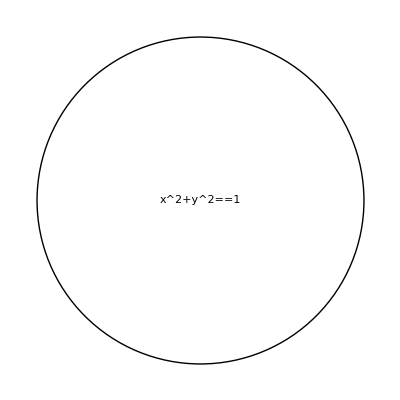

```mathematica
Graphics[{Circle[],Inset["x^2+y^2==1",{0,0}]}]
```

```mathematica
Dynamic Elements - Dynamic
```

```mathematica
Slider[Dynamic[x]]
```

### Importing / Exporting

```mathematica
Import
```

```mathematica
Import["C:\\Users\\Ded\\Desktop\\13.jpg"]
```

-Graphics-

```mathematica
Export
```

```mathematica
Export[LocalObject["plot"],Plot[Sin[x],{x,0,10}],"PNG"]
```

LocalObject[file:///C:/Users/Ded/AppData/Roaming/Wolfram/Objects/plot]

```mathematica
Import[%]
```

-Graphics-

## Anatomy Visualization

### AnatomyPlot3D

```mathematica
AnatomyPlot3D[{Entity["AnatomicalStructure","Skeleton"]}]
```

-Graphics3D-

weather forecast

WolframAlphaQueryResults

Загружаем изображение стакана. Используя функцию ImageContents выбираем загруженное изображение и минимальное допустимое значение для распознавания ставим 0.25. 
Функция распознала что это стакан  с вероятность 0.814... Распознавание работает.

```mathematica
image = -Graphics-
```

-Graphics-

```mathematica
objects = ImageContents[image, AcceptanceThreshold -> .25]
```

Dataset[<>]